# Horizontal Pendulum with Springs and Excitation

-Graphics-

```mathematica
ClearAll["Global`*"]
$Assumptions={m>0&&Subscript[F, _]>0&&L>0&&kTorsional >0&&kLinear>0}
```

{m>0&&F__>0&&L>0&&kTorsional>0&&kLinear>0}

## Equations of Motion

This pendulum is a system of four equal masses:

```mathematica
massQuantity = 4;
```

Assuming θ is the angle measured from the horizontal axis. I define position vectors for all masses:

```mathematica
Subscript[r, 1]={L Cos[Subscript[θ, 1][t]],L Sin[Subscript[θ, 1][t]]};
Subscript[r, 2]={Subscript[r, 1][[1]]+L Cos[Subscript[θ, 2][t]],Subscript[r, 1][[2]]+L Sin[Subscript[θ, 2][t]]};
Subscript[r, 3]={Subscript[r, 2][[1]]+L Cos[Subscript[θ, 3][t]],Subscript[r, 2][[2]]+L Sin[Subscript[θ, 3][t]]};
Subscript[r, 4]={Subscript[r, 3][[1]]+L Cos[Subscript[θ, 4][t]],Subscript[r, 3][[2]]+L Sin[Subscript[θ, 4][t]]};
```

Given that T = 1/2 m v^2, define the kinetic energy of a system:

```mathematica
KE=Sum[1/2 m(D[Subscript[r, k][[1]],t]^2+D[Subscript[r, k][[2]],t]^2),{k,massQuantity}]//FullSimplify
```

1/2 L^2 m (4 θ_1'[t]^2+3 θ_2'[t]^2+4 Cos[θ_2[t]-θ_3[t]] θ_2'[t] θ_3'[t]+2 θ_3'[t]^2+2 (Cos[θ_2[t]-θ_4[t]] θ_2'[t]+Cos[θ_3[t]-θ_4[t]] θ_3'[t]) θ_4'[t]+θ_4'[t]^2+2 θ_1'[t] (3 Cos[θ_1[t]-θ_2[t]] θ_2'[t]+2 Cos[θ_1[t]-θ_3[t]] θ_3'[t]+Cos[θ_1[t]-θ_4[t]] θ_4'[t]))

Given V_gravity=m g h, V_(torsional spring)=1/2 kTorsional θ^2, V_(linear spring)=1/2 kLinear x^2. Define potential energy of a system:

```mathematica
PE=Sum[{0,m g}.{ Subscript[r, k][[1]],Subscript[r, k][[2]]},{k,massQuantity}]+Sum[.5kTorsional (Subscript[θ, k][t])^2,{k,massQuantity}]+.5 kLinear (Subscript[r, 4][[2]])^2//Simplify
```

g L m Sin[θ_1[t]]+g L m (Sin[θ_1[t]]+Sin[θ_2[t]])+g L m (Sin[θ_1[t]]+Sin[θ_2[t]]+Sin[θ_3[t]])+g L m (Sin[θ_1[t]]+Sin[θ_2[t]]+Sin[θ_3[t]]+Sin[θ_4[t]])+0.5 kLinear L^2 (Sin[θ_1[t]]+Sin[θ_2[t]]+Sin[θ_3[t]]+Sin[θ_4[t]])^2+0.5 kTorsional θ_1[t]^2+0.5 kTorsional θ_2[t]^2+0.5 kTorsional θ_3[t]^2+0.5 kTorsional θ_4[t]^2

Using Equation 6.33 from the book, the Lagrange equation is defined as:

```mathematica
Lg=KE-PE //Simplify
```

-g L m Sin[θ_1[t]]-g L m (Sin[θ_1[t]]+Sin[θ_2[t]])-g L m (Sin[θ_1[t]]+Sin[θ_2[t]]+Sin[θ_3[t]])-g L m (Sin[θ_1[t]]+Sin[θ_2[t]]+Sin[θ_3[t]]+Sin[θ_4[t]])-0.5 kLinear L^2 (Sin[θ_1[t]]+Sin[θ_2[t]]+Sin[θ_3[t]]+Sin[θ_4[t]])^2-0.5 kTorsional θ_1[t]^2-0.5 kTorsional θ_2[t]^2-0.5 kTorsional θ_3[t]^2-0.5 kTorsional θ_4[t]^2+1/2 L^2 m (4 θ_1'[t]^2+3 θ_2'[t]^2+4 Cos[θ_2[t]-θ_3[t]] θ_2'[t] θ_3'[t]+2 θ_3'[t]^2+2 (Cos[θ_2[t]-θ_4[t]] θ_2'[t]+Cos[θ_3[t]-θ_4[t]] θ_3'[t]) θ_4'[t]+θ_4'[t]^2+2 θ_1'[t] (3 Cos[θ_1[t]-θ_2[t]] θ_2'[t]+2 Cos[θ_1[t]-θ_3[t]] θ_3'[t]+Cos[θ_1[t]-θ_4[t]] θ_4'[t]))

Define virtual work of a system:

```mathematica
δW = {0,F[t]}. D[{Subscript[r, 2][[1]],Subscript[r, 2][[2]]},t]/.Subscript[θ, n_]'[t]-> Subscript[δθ, n]//Expand
```

L Cos[θ_1[t]] F[t] δθ_1+L Cos[θ_2[t]] F[t] δθ_2

Preallocate memory for the equations of motion:

```mathematica
eq={Null,Null,Null,Null};
```

Using Equation 6.42 from the book, the equations of motion are:

```mathematica
Scan[
Print[
Subscript[eq, #]=Expand[
D[D[Lg,Subscript[θ, #]'[t]],t]-D[Lg,Subscript[θ, #][t]]==Coefficient[δW,Subscript[δθ, #]]
]] &, {1,2,3,4}]
```

4 g L m Cos[θ_1[t]]+1. kLinear L^2 Cos[θ_1[t]] Sin[θ_1[t]]+1. kLinear L^2 Cos[θ_1[t]] Sin[θ_2[t]]+1. kLinear L^2 Cos[θ_1[t]] Sin[θ_3[t]]+1. kLinear L^2 Cos[θ_1[t]] Sin[θ_4[t]]+1. kTorsional θ_1[t]+3 L^2 m Sin[θ_1[t]-θ_2[t]] θ_2'[t]^2+2 L^2 m Sin[θ_1[t]-θ_3[t]] θ_3'[t]^2+L^2 m Sin[θ_1[t]-θ_4[t]] θ_4'[t]^2+4 L^2 m θ_1''[t]+3 L^2 m Cos[θ_1[t]-θ_2[t]] θ_2''[t]+2 L^2 m Cos[θ_1[t]-θ_3[t]] θ_3''[t]+L^2 m Cos[θ_1[t]-θ_4[t]] θ_4''[t]==L Cos[θ_1[t]] F[t]

3 g L m Cos[θ_2[t]]+1. kLinear L^2 Cos[θ_2[t]] Sin[θ_1[t]]+1. kLinear L^2 Cos[θ_2[t]] Sin[θ_2[t]]+1. kLinear L^2 Cos[θ_2[t]] Sin[θ_3[t]]+1. kLinear L^2 Cos[θ_2[t]] Sin[θ_4[t]]+1. kTorsional θ_2[t]-3 L^2 m Sin[θ_1[t]-θ_2[t]] θ_1'[t]^2+2 L^2 m Sin[θ_2[t]-θ_3[t]] θ_3'[t]^2+L^2 m Sin[θ_2[t]-θ_4[t]] θ_4'[t]^2+3 L^2 m Cos[θ_1[t]-θ_2[t]] θ_1''[t]+3 L^2 m θ_2''[t]+2 L^2 m Cos[θ_2[t]-θ_3[t]] θ_3''[t]+L^2 m Cos[θ_2[t]-θ_4[t]] θ_4''[t]==L Cos[θ_2[t]] F[t]

2 g L m Cos[θ_3[t]]+1. kLinear L^2 Cos[θ_3[t]] Sin[θ_1[t]]+1. kLinear L^2 Cos[θ_3[t]] Sin[θ_2[t]]+1. kLinear L^2 Cos[θ_3[t]] Sin[θ_3[t]]+1. kLinear L^2 Cos[θ_3[t]] Sin[θ_4[t]]+1. kTorsional θ_3[t]-2 L^2 m Sin[θ_1[t]-θ_3[t]] θ_1'[t]^2-2 L^2 m Sin[θ_2[t]-θ_3[t]] θ_2'[t]^2+L^2 m Sin[θ_3[t]-θ_4[t]] θ_4'[t]^2+2 L^2 m Cos[θ_1[t]-θ_3[t]] θ_1''[t]+2 L^2 m Cos[θ_2[t]-θ_3[t]] θ_2''[t]+2 L^2 m θ_3''[t]+L^2 m Cos[θ_3[t]-θ_4[t]] θ_4''[t]==0

g L m Cos[θ_4[t]]+1. kLinear L^2 Cos[θ_4[t]] Sin[θ_1[t]]+1. kLinear L^2 Cos[θ_4[t]] Sin[θ_2[t]]+1. kLinear L^2 Cos[θ_4[t]] Sin[θ_3[t]]+1. kLinear L^2 Cos[θ_4[t]] Sin[θ_4[t]]+1. kTorsional θ_4[t]-L^2 m Sin[θ_1[t]-θ_4[t]] θ_1'[t]^2-L^2 m Sin[θ_2[t]-θ_4[t]] θ_2'[t]^2-L^2 m Sin[θ_3[t]-θ_4[t]] θ_3'[t]^2+L^2 m Cos[θ_1[t]-θ_4[t]] θ_1''[t]+L^2 m Cos[θ_2[t]-θ_4[t]] θ_2''[t]+L^2 m Cos[θ_3[t]-θ_4[t]] θ_3''[t]+L^2 m θ_4''[t]==0

## Equilibrium Points

The problem statement defines the static equilibrium when the bars are in the horizontal configuration under the action of gravity and due  to the pretension in both the torsional and linear springs. Thus, thetas at equilibrium are defined as θ_1=θ_2=θ_3=θ_4=0.

```mathematica
EqRules={Subscript[θ, _]'[t]->0,Subscript[θ, _]''[t]->0,F[t]->0};
```

```mathematica
EqEqs={Subscript[eq, 1],Subscript[eq, 2],Subscript[eq, 3],Subscript[eq, 4]}/.EqRules
```

{4 g L m Cos[θ_1[t]]+1. kLinear L^2 Cos[θ_1[t]] Sin[θ_1[t]]+1. kLinear L^2 Cos[θ_1[t]] Sin[θ_2[t]]+1. kLinear L^2 Cos[θ_1[t]] Sin[θ_3[t]]+1. kLinear L^2 Cos[θ_1[t]] Sin[θ_4[t]]+1. kTorsional θ_1[t]==0,3 g L m Cos[θ_2[t]]+1. kLinear L^2 Cos[θ_2[t]] Sin[θ_1[t]]+1. kLinear L^2 Cos[θ_2[t]] Sin[θ_2[t]]+1. kLinear L^2 Cos[θ_2[t]] Sin[θ_3[t]]+1. kLinear L^2 Cos[θ_2[t]] Sin[θ_4[t]]+1. kTorsional θ_2[t]==0,2 g L m Cos[θ_3[t]]+1. kLinear L^2 Cos[θ_3[t]] Sin[θ_1[t]]+1. kLinear L^2 Cos[θ_3[t]] Sin[θ_2[t]]+1. kLinear L^2 Cos[θ_3[t]] Sin[θ_3[t]]+1. kLinear L^2 Cos[θ_3[t]] Sin[θ_4[t]]+1. kTorsional θ_3[t]==0,g L m Cos[θ_4[t]]+1. kLinear L^2 Cos[θ_4[t]] Sin[θ_1[t]]+1. kLinear L^2 Cos[θ_4[t]] Sin[θ_2[t]]+1. kLinear L^2 Cos[θ_4[t]] Sin[θ_3[t]]+1. kLinear L^2 Cos[θ_4[t]] Sin[θ_4[t]]+1. kTorsional θ_4[t]==0}

## Linearized Equations of Motion About Equilibrium Points

Prepare for linearization about a general equilibrium point (θe_1, θe_2, θe_3, θe_4) (this is a trick to do multivariate Taylor expansion):

```mathematica
subs=Join[
Table[Subscript[θ, k][t]-> Subscript[θe, k]+q Subscript[θ, k][t],{k,massQuantity}],Table[Subscript[θ, k]'[t]-> q Subscript[θ, k]'[t],{k,massQuantity}],
Table[Subscript[θ, k]''[t]-> q Subscript[θ, k]''[t],{k,massQuantity}]]
```

{θ_1[t]→θe_1+q θ_1[t],θ_2[t]→θe_2+q θ_2[t],θ_3[t]→θe_3+q θ_3[t],θ_4[t]→θe_4+q θ_4[t],θ_1'[t]→q θ_1'[t],θ_2'[t]→q θ_2'[t],θ_3'[t]→q θ_3'[t],θ_4'[t]→q θ_4'[t],θ_1''[t]→q θ_1''[t],θ_2''[t]→q θ_2''[t],θ_3''[t]→q θ_3''[t],θ_4''[t]→q θ_4''[t]}

Linearize equations (use the trick):

```mathematica
Do[Print[Subscript[Eq, k]=Normal[Series[Subscript[eq, k]/.subs,{q,0,1}]]/.q-> 1],{k,massQuantity}]
```

4 g L m Cos[θe_1]+1. kLinear L^2 Cos[θe_1] Sin[θe_1]+1. kLinear L^2 Cos[θe_1] Sin[θe_2]+1. kLinear L^2 Cos[θe_1] Sin[θe_3]+1. kLinear L^2 Cos[θe_1] Sin[θe_4]+1. kTorsional θe_1+1. kTorsional θ_1[t]-4 g L m Sin[θe_1] θ_1[t]+1. kLinear L^2 (Cos[θe_1]^2 θ_1[t]-Sin[θe_1]^2 θ_1[t])+1. kLinear L^2 (-Sin[θe_1] Sin[θe_2] θ_1[t]+Cos[θe_1] Cos[θe_2] θ_2[t])+1. kLinear L^2 (-Sin[θe_1] Sin[θe_3] θ_1[t]+Cos[θe_1] Cos[θe_3] θ_3[t])+1. kLinear L^2 (-Sin[θe_1] Sin[θe_4] θ_1[t]+Cos[θe_1] Cos[θe_4] θ_4[t])+4 L^2 m θ_1''[t]+3 L^2 m Cos[θe_1-θe_2] θ_2''[t]+2 L^2 m Cos[θe_1-θe_3] θ_3''[t]+L^2 m Cos[θe_1-θe_4] θ_4''[t]==L Cos[θe_1] F[t]-L F[t] Sin[θe_1] θ_1[t]

3 g L m Cos[θe_2]+1. kLinear L^2 Cos[θe_2] Sin[θe_1]+1. kLinear L^2 Cos[θe_2] Sin[θe_2]+1. kLinear L^2 Cos[θe_2] Sin[θe_3]+1. kLinear L^2 Cos[θe_2] Sin[θe_4]+1. kTorsional θe_2+1. kTorsional θ_2[t]-3 g L m Sin[θe_2] θ_2[t]+1. kLinear L^2 (Cos[θe_1] Cos[θe_2] θ_1[t]-Sin[θe_1] Sin[θe_2] θ_2[t])+1. kLinear L^2 (Cos[θe_2]^2 θ_2[t]-Sin[θe_2]^2 θ_2[t])+1. kLinear L^2 (-Sin[θe_2] Sin[θe_3] θ_2[t]+Cos[θe_2] Cos[θe_3] θ_3[t])+1. kLinear L^2 (-Sin[θe_2] Sin[θe_4] θ_2[t]+Cos[θe_2] Cos[θe_4] θ_4[t])+3 L^2 m Cos[θe_1-θe_2] θ_1''[t]+3 L^2 m θ_2''[t]+2 L^2 m Cos[θe_2-θe_3] θ_3''[t]+L^2 m Cos[θe_2-θe_4] θ_4''[t]==L Cos[θe_2] F[t]-L F[t] Sin[θe_2] θ_2[t]

2 g L m Cos[θe_3]+1. kLinear L^2 Cos[θe_3] Sin[θe_1]+1. kLinear L^2 Cos[θe_3] Sin[θe_2]+1. kLinear L^2 Cos[θe_3] Sin[θe_3]+1. kLinear L^2 Cos[θe_3] Sin[θe_4]+1. kTorsional θe_3+1. kTorsional θ_3[t]-2 g L m Sin[θe_3] θ_3[t]+1. kLinear L^2 (Cos[θe_1] Cos[θe_3] θ_1[t]-Sin[θe_1] Sin[θe_3] θ_3[t])+1. kLinear L^2 (Cos[θe_2] Cos[θe_3] θ_2[t]-Sin[θe_2] Sin[θe_3] θ_3[t])+1. kLinear L^2 (Cos[θe_3]^2 θ_3[t]-Sin[θe_3]^2 θ_3[t])+1. kLinear L^2 (-Sin[θe_3] Sin[θe_4] θ_3[t]+Cos[θe_3] Cos[θe_4] θ_4[t])+2 L^2 m Cos[θe_1-θe_3] θ_1''[t]+2 L^2 m Cos[θe_2-θe_3] θ_2''[t]+2 L^2 m θ_3''[t]+L^2 m Cos[θe_3-θe_4] θ_4''[t]==0

g L m Cos[θe_4]+1. kLinear L^2 Cos[θe_4] Sin[θe_1]+1. kLinear L^2 Cos[θe_4] Sin[θe_2]+1. kLinear L^2 Cos[θe_4] Sin[θe_3]+1. kLinear L^2 Cos[θe_4] Sin[θe_4]+1. kTorsional θe_4+1. kTorsional θ_4[t]-g L m Sin[θe_4] θ_4[t]+1. kLinear L^2 (Cos[θe_1] Cos[θe_4] θ_1[t]-Sin[θe_1] Sin[θe_4] θ_4[t])+1. kLinear L^2 (Cos[θe_2] Cos[θe_4] θ_2[t]-Sin[θe_2] Sin[θe_4] θ_4[t])+1. kLinear L^2 (Cos[θe_3] Cos[θe_4] θ_3[t]-Sin[θe_3] Sin[θe_4] θ_4[t])+1. kLinear L^2 (Cos[θe_4]^2 θ_4[t]-Sin[θe_4]^2 θ_4[t])+L^2 m Cos[θe_1-θe_4] θ_1''[t]+L^2 m Cos[θe_2-θe_4] θ_2''[t]+L^2 m Cos[θe_3-θe_4] θ_3''[t]+L^2 m θ_4''[t]==0

Then the linearized equations of motions about some equilibrium point (θe_1, θe_2, θe_3, θe_4) are:

```mathematica
Do[Print[Subscript[Eq, k]=(Subscript[Eq, k]/.subs)],{k,massQuantity}]
```

4 g L m Cos[θe_1]+1. kLinear L^2 Cos[θe_1] Sin[θe_1]+1. kLinear L^2 Cos[θe_1] Sin[θe_2]+1. kLinear L^2 Cos[θe_1] Sin[θe_3]+1. kLinear L^2 Cos[θe_1] Sin[θe_4]+1. kTorsional θe_1+1. kTorsional (θe_1+q θ_1[t])-4 g L m Sin[θe_1] (θe_1+q θ_1[t])+1. kLinear L^2 (Cos[θe_1]^2 (θe_1+q θ_1[t])-Sin[θe_1]^2 (θe_1+q θ_1[t]))+1. kLinear L^2 (-Sin[θe_1] Sin[θe_2] (θe_1+q θ_1[t])+Cos[θe_1] Cos[θe_2] (θe_2+q θ_2[t]))+1. kLinear L^2 (-Sin[θe_1] Sin[θe_3] (θe_1+q θ_1[t])+Cos[θe_1] Cos[θe_3] (θe_3+q θ_3[t]))+1. kLinear L^2 (-Sin[θe_1] Sin[θe_4] (θe_1+q θ_1[t])+Cos[θe_1] Cos[θe_4] (θe_4+q θ_4[t]))+4 L^2 m q θ_1''[t]+3 L^2 m q Cos[θe_1-θe_2] θ_2''[t]+2 L^2 m q Cos[θe_1-θe_3] θ_3''[t]+L^2 m q Cos[θe_1-θe_4] θ_4''[t]==L Cos[θe_1] F[t]-L F[t] Sin[θe_1] (θe_1+q θ_1[t])

3 g L m Cos[θe_2]+1. kLinear L^2 Cos[θe_2] Sin[θe_1]+1. kLinear L^2 Cos[θe_2] Sin[θe_2]+1. kLinear L^2 Cos[θe_2] Sin[θe_3]+1. kLinear L^2 Cos[θe_2] Sin[θe_4]+1. kTorsional θe_2+1. kTorsional (θe_2+q θ_2[t])-3 g L m Sin[θe_2] (θe_2+q θ_2[t])+1. kLinear L^2 (Cos[θe_1] Cos[θe_2] (θe_1+q θ_1[t])-Sin[θe_1] Sin[θe_2] (θe_2+q θ_2[t]))+1. kLinear L^2 (Cos[θe_2]^2 (θe_2+q θ_2[t])-Sin[θe_2]^2 (θe_2+q θ_2[t]))+1. kLinear L^2 (-Sin[θe_2] Sin[θe_3] (θe_2+q θ_2[t])+Cos[θe_2] Cos[θe_3] (θe_3+q θ_3[t]))+1. kLinear L^2 (-Sin[θe_2] Sin[θe_4] (θe_2+q θ_2[t])+Cos[θe_2] Cos[θe_4] (θe_4+q θ_4[t]))+3 L^2 m q Cos[θe_1-θe_2] θ_1''[t]+3 L^2 m q θ_2''[t]+2 L^2 m q Cos[θe_2-θe_3] θ_3''[t]+L^2 m q Cos[θe_2-θe_4] θ_4''[t]==L Cos[θe_2] F[t]-L F[t] Sin[θe_2] (θe_2+q θ_2[t])

2 g L m Cos[θe_3]+1. kLinear L^2 Cos[θe_3] Sin[θe_1]+1. kLinear L^2 Cos[θe_3] Sin[θe_2]+1. kLinear L^2 Cos[θe_3] Sin[θe_3]+1. kLinear L^2 Cos[θe_3] Sin[θe_4]+1. kTorsional θe_3+1. kTorsional (θe_3+q θ_3[t])-2 g L m Sin[θe_3] (θe_3+q θ_3[t])+1. kLinear L^2 (Cos[θe_1] Cos[θe_3] (θe_1+q θ_1[t])-Sin[θe_1] Sin[θe_3] (θe_3+q θ_3[t]))+1. kLinear L^2 (Cos[θe_2] Cos[θe_3] (θe_2+q θ_2[t])-Sin[θe_2] Sin[θe_3] (θe_3+q θ_3[t]))+1. kLinear L^2 (Cos[θe_3]^2 (θe_3+q θ_3[t])-Sin[θe_3]^2 (θe_3+q θ_3[t]))+1. kLinear L^2 (-Sin[θe_3] Sin[θe_4] (θe_3+q θ_3[t])+Cos[θe_3] Cos[θe_4] (θe_4+q θ_4[t]))+2 L^2 m q Cos[θe_1-θe_3] θ_1''[t]+2 L^2 m q Cos[θe_2-θe_3] θ_2''[t]+2 L^2 m q θ_3''[t]+L^2 m q Cos[θe_3-θe_4] θ_4''[t]==0

g L m Cos[θe_4]+1. kLinear L^2 Cos[θe_4] Sin[θe_1]+1. kLinear L^2 Cos[θe_4] Sin[θe_2]+1. kLinear L^2 Cos[θe_4] Sin[θe_3]+1. kLinear L^2 Cos[θe_4] Sin[θe_4]+1. kTorsional θe_4+1. kTorsional (θe_4+q θ_4[t])-g L m Sin[θe_4] (θe_4+q θ_4[t])+1. kLinear L^2 (Cos[θe_1] Cos[θe_4] (θe_1+q θ_1[t])-Sin[θe_1] Sin[θe_4] (θe_4+q θ_4[t]))+1. kLinear L^2 (Cos[θe_2] Cos[θe_4] (θe_2+q θ_2[t])-Sin[θe_2] Sin[θe_4] (θe_4+q θ_4[t]))+1. kLinear L^2 (Cos[θe_3] Cos[θe_4] (θe_3+q θ_3[t])-Sin[θe_3] Sin[θe_4] (θe_4+q θ_4[t]))+1. kLinear L^2 (Cos[θe_4]^2 (θe_4+q θ_4[t])-Sin[θe_4]^2 (θe_4+q θ_4[t]))+L^2 m q Cos[θe_1-θe_4] θ_1''[t]+L^2 m q Cos[θe_2-θe_4] θ_2''[t]+L^2 m q Cos[θe_3-θe_4] θ_3''[t]+L^2 m q θ_4''[t]==0

The equations of motion for small oscillations about the stable equilibrium (0,0,0,0) are:

```mathematica
EqMotion=Table[Subscript[Eq, k],{k,massQuantity}]/.{Subscript[θe, _]->0}/.q-> 1
```

{0.+4 g L m+1. kTorsional θ_1[t]+1. kLinear L^2 θ_1[t]+1. kLinear L^2 θ_2[t]+1. kLinear L^2 θ_3[t]+1. kLinear L^2 θ_4[t]+4 L^2 m θ_1''[t]+3 L^2 m θ_2''[t]+2 L^2 m θ_3''[t]+L^2 m θ_4''[t]==L F[t],0.+3 g L m+1. kLinear L^2 θ_1[t]+1. kTorsional θ_2[t]+1. kLinear L^2 θ_2[t]+1. kLinear L^2 θ_3[t]+1. kLinear L^2 θ_4[t]+3 L^2 m θ_1''[t]+3 L^2 m θ_2''[t]+2 L^2 m θ_3''[t]+L^2 m θ_4''[t]==L F[t],0.+2 g L m+1. kLinear L^2 θ_1[t]+1. kLinear L^2 θ_2[t]+1. kTorsional θ_3[t]+1. kLinear L^2 θ_3[t]+1. kLinear L^2 θ_4[t]+2 L^2 m θ_1''[t]+2 L^2 m θ_2''[t]+2 L^2 m θ_3''[t]+L^2 m θ_4''[t]==0,0.+g L m+1. kLinear L^2 θ_1[t]+1. kLinear L^2 θ_2[t]+1. kLinear L^2 θ_3[t]+1. kTorsional θ_4[t]+1. kLinear L^2 θ_4[t]+L^2 m θ_1''[t]+L^2 m θ_2''[t]+L^2 m θ_3''[t]+L^2 m θ_4''[t]==0}

## Modal Analysis

Use simple parameter assignments as given in the problem:

```mathematica
EqMotion= EqMotion/.kTorsional-> 70 kLinear L^2;
```

The equations of motion for small oscillations about the stable equilibrium are:

```mathematica
Mm=Normal[CoefficientArrays[EqMotion,Table[Subscript[θ, k]''[t],{k,massQuantity}]]][[2]]/(L^2 m); Mm//MatrixForm
Km=Normal[CoefficientArrays[EqMotion,Table[Subscript[θ, k][t],{k,massQuantity}]]][[2]]/(L^2 m); Km //MatrixForm
Fm=EqMotion[[All,2]]/(L);Fm//MatrixForm
```

(4. | 3. | 2. | 1
3. | 3. | 2. | 1
2. | 2. | 2. | 1
1 | 1 | 1 | 1)

((71. kLinear)/m | (1. kLinear)/m | (1. kLinear)/m | (1. kLinear)/m
(1. kLinear)/m | (71. kLinear)/m | (1. kLinear)/m | (1. kLinear)/m
(1. kLinear)/m | (1. kLinear)/m | (71. kLinear)/m | (1. kLinear)/m
(1. kLinear)/m | (1. kLinear)/m | (1. kLinear)/m | (71. kLinear)/m)

(F[t]
F[t]
0
0)

Below are the eigenvectors of the system:

```mathematica
EqualMassES=Eigensystem[{m/kLinear Km,Mm}//N]
```

{{247.299,164.495,70.3349,8.87114},{{-0.227753,0.57686,-0.656479,0.429415},{0.428134,-0.577952,-0.225888,0.656999},{0.577357,-0.00276235,-0.580106,-0.574568},{0.664019,0.579867,0.422229,0.211081}}}

## Natural Frequencies and Normal Modes

Normal modes:

```mathematica
EqualMassNM=EqualMassES[[2]]
```

{{-0.227753,0.57686,-0.656479,0.429415},{0.428134,-0.577952,-0.225888,0.656999},{0.577357,-0.00276235,-0.580106,-0.574568},{0.664019,0.579867,0.422229,0.211081}}

Natural frequencies:

```mathematica
EqualMassω=√(EqualMassES[[1]] kLinear/m)//MatrixForm
```

(15.7257 √(kLinear/m)
12.8256 √(kLinear/m)
8.38659 √(kLinear/m)
2.97845 √(kLinear/m))

Plot modes:

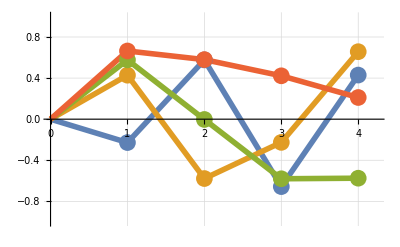

```mathematica
plt = Show[ListLinePlot[Table[Thread[{{0,1,2,3,4},Insert[EqualMassNM,0,{{1,1},{2,1},{3,1},{4,1}}][[k]]}],{k,4}],PlotStyle->{Thickness[0.01]},GridLines->Automatic,PlotRange->{{0,4.25},{-1,1}}],ListPlot[Table[Thread[{{1,2,3,4},EqualMassNM[[k]]}],{k,4}],PlotStyle->PointSize[0.03],GridLines->Automatic]]
```

## Frequency Response to Excitations

Derive and plot the frequency response functions for each mass when excited by F(t) = Fe^(i w t) and plot them.

Using equation for 5.97 from the book:

```mathematica
Zω = -ω^2 Mm +m/kLinear Km
```

{{71.-4. ω^2,1.-3. ω^2,1.-2. ω^2,1.-ω^2},{1.-3. ω^2,71.-3. ω^2,1.-2. ω^2,1.-ω^2},{1.-2. ω^2,1.-2. ω^2,71.-2. ω^2,1.-ω^2},{1.-ω^2,1.-ω^2,1.-ω^2,71.-ω^2}}

Using the method similar to equation 5.100 from the book:

```mathematica
ZωInverse = Inverse[Zω]//Simplify;
```

Using equation 5.99 from the book:

```mathematica
Xω= ZωInverse.Fm/.F[t]->1//Simplify
```

{(352800.-14770. ω^2+70. ω^4)/(2.5382×10^7-3.479×10^6 ω^2+73920. ω^4-491. ω^6+1. ω^8),(352800.-19810. ω^2+281. ω^4-1. ω^6)/(2.5382×10^7-3.479×10^6 ω^2+73920. ω^4-491. ω^6+1. ω^8),(-9800.+19810. ω^2-281. ω^4+1. ω^6)/(2.5382×10^7-3.479×10^6 ω^2+73920. ω^4-491. ω^6+1. ω^8),(-9800.+9870. ω^2-70. ω^4)/(2.5382×10^7-3.479×10^6 ω^2+73920. ω^4-491. ω^6+1. ω^8)}

The plot of the frequency response function at the first mass:

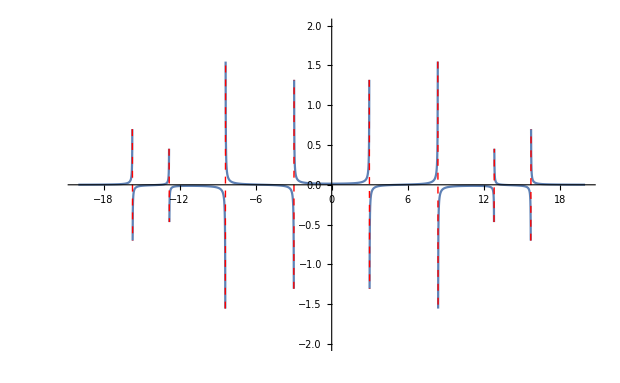

```mathematica
Plot[Xω[[1]],{ω,-20,20},PlotRange->{-2,2},ExclusionsStyle->Directive[Red,Dashed]]
```

The plot of the frequency response function at the second mass:

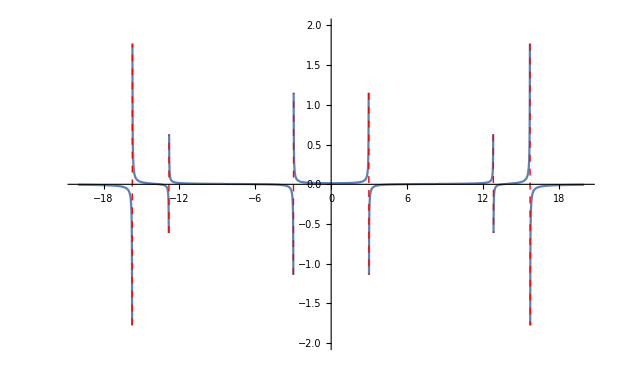

```mathematica
Plot[Xω[[2]],{ω,-20,20},PlotRange->{-2,2},ExclusionsStyle->Directive[Red,Dashed]]
```

The plot of the frequency response function at the third mass:

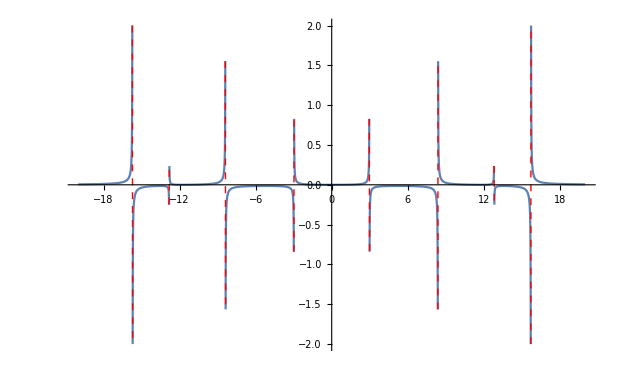

```mathematica
Plot[Xω[[3]],{ω,-20,20},PlotRange->{-2,2},ExclusionsStyle->Directive[Red,Dashed]]
```

The plot of the frequency response function at the fourth mass:

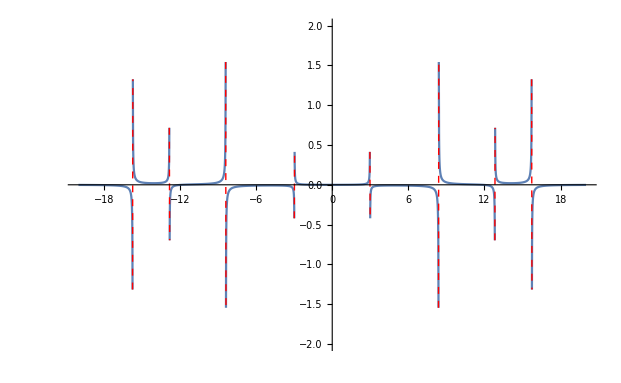

```mathematica
Plot[Xω[[4]],{ω,-20,20},PlotRange->{-2,2},ExclusionsStyle->Directive[Red,Dashed]]
```

## Displacement Amplitudes of the Steady State Response

For Ω = 0.7ω_2 and Ω = 0.99ω_2 plot the displacement amplitudes of the steady state response and compare them to the second mode shape.

Using equation 7.199 from the book:

```mathematica
Qt70 = ZωInverse Cos[ω t]/.ω-> (.7*(EqualMassES[[1]][[3]])^.5)
```

{{0.0113836 Cos[5.87061 t],-0.00850678 Cos[5.87061 t],-0.00992315 Cos[5.87061 t],-0.00645392 Cos[5.87061 t]},{-0.00850678 Cos[5.87061 t],0.0099672 Cos[5.87061 t],-0.00503754 Cos[5.87061 t],-0.00327637 Cos[5.87061 t]},{-0.00992315 Cos[5.87061 t],-0.00503754 Cos[5.87061 t],0.016614 Cos[5.87061 t],0.00151429 Cos[5.87061 t]},{-0.00645392 Cos[5.87061 t],-0.00327637 Cos[5.87061 t],0.00151429 Cos[5.87061 t],0.0198451 Cos[5.87061 t]}}

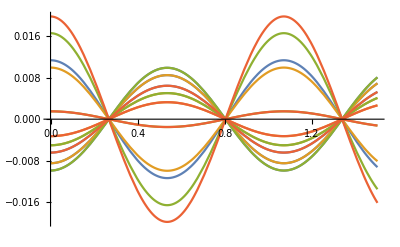

```mathematica
Plot[{Qt70[[1]],Qt70[[2]],Qt70[[3]],Qt70[[4]],},{t,0,1.5}]
```

The behavior of the curves on this plot are very similar to the form of the second mode. There is no damping in the system, so it will continue in this manner indefinitely.

```mathematica
Qt99 = ZωInverse Cos[ω t]/.ω-> (.99*(EqualMassES[[1]][[3]])^.5)
```

{{0.242796 Cos[8.30273 t],-0.0105926 Cos[8.30273 t],-0.239264 Cos[8.30273 t],-0.232311 Cos[8.30273 t]},{-0.0105926 Cos[8.30273 t],0.0141246 Cos[8.30273 t],-0.00363939 Cos[8.30273 t],-0.00353362 Cos[8.30273 t]},{-0.239264 Cos[8.30273 t],-0.00363939 Cos[8.30273 t],0.249855 Cos[8.30273 t],0.228724 Cos[8.30273 t]},{-0.232311 Cos[8.30273 t],-0.00353362 Cos[8.30273 t],0.228724 Cos[8.30273 t],0.250022 Cos[8.30273 t]}}

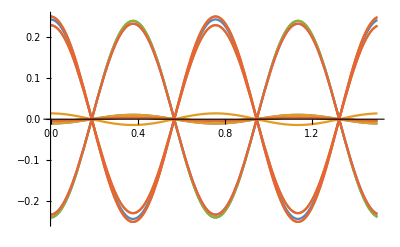

```mathematica
Plot[{Qt99[[1]],Qt99[[2]],Qt99[[3]],Qt99[[4]],},{t,0,1.5}]
```

The behavior of the curves on this plot are unlike the form of the second mode. This is likely due to the fact that the excitation frequency is near a natural frequency, namely the second natural frequency.